```mathematica
Quit
```

## Static

### Labeled rectangle

```mathematica
toGraphic[myRectangle[leftDown_, rightUp_, label_]]:={Rectangle[leftDown,rightUp],Text[Style[label,Red],(leftDown+rightUp)/2.]}
toGraphic[list_List]:=Flatten[Map[toGraphic,list]];

myRectangle[leftDown_,rightUp_,id_]["LeftDown"]:=leftDown;
myRectangle[leftDown_,rightUp_,id_]["RightUp"]:=rightUp;
myRectangle[leftDown_,rightUp_,id_]["Id"]:=id

myRectangle/:toRectangle[myRectangle[leftDown_,rightUp_,id_]]:=Rectangle[leftDown,rightUp]
SetAttributes[toRectangle,Listable]

myRectangle/:myArea[myRectangle[leftDown_,rightUp_,id_]]:=Times@@(leftDown-rightUp)

myRectangle/:myCentroid[myRectangle[leftDown_,rightUp_,id_]]:=1/2(myRectangle[leftDown,rightUp,id]["LeftDown"]+myRectangle[leftDown,rightUp,id]["RightUp"])
SetAttributes[myCentroid,Listable]

myRectangle/:myTranslate[myRectangle[leftDown_,rightUp_,id_],vec_List]:=myRectangle[leftDown+vec,rightUp+vec,id]

myRectangle/:myScaling[myRectangle[leftDown_,rightUp_,id_],scale_]:=myRectangle[leftDown*scale,rightUp*scale,id]
```

### Generating the word lists

```mathematica
dataLength=5;

xPos=RandomReal[{5,10},dataLength];
yPos=RandomReal[{1,5},dataLength];

$currentID=0;
ID[]:=(IntegerString[$currentID++,10,3]);
wordList1=Table[myRectangle[{-x,-y},{x,y},ID[]],{x,xPos},{y,yPos}]//Flatten;

wordList2=myScaling[#,RandomReal[{0.5,1}]]&/@wordList1;
```

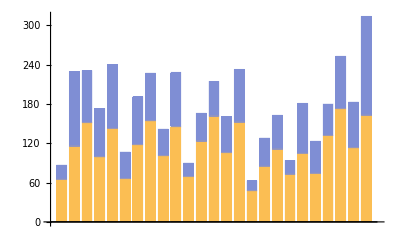

```mathematica
BarChart[{myArea/@wordList1,myArea/@wordList2}//Transpose,ChartLayout->"Stacked"]
```

### Spiral girds

```mathematica
θMaxVal=2.00 10^4;
ΔθVal=10.00;

bValue[wordList_,θMax_:θMaxVal]:=3/4(√Total[myArea/@wordList])/θMax;

gridPoint[θ_]:={b θ Cos[θ/180],b θ Sin[θ/180]}

spiralGrid[wordList_,θMax_:θMaxVal,Δθ_:ΔθVal]:=Module[{bSub=bValue[wordList,θMax]},Table[gridPoint[θ],{θ,Δθ,θMax,Δθ}]/.b->bSub]
```

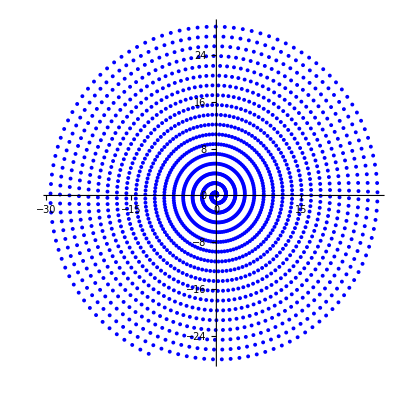

```mathematica
plot1=ListPlot[spiralGrid[wordList2],AspectRatio->1,PlotStyle->{PointSize[0.007],Blue}]
```

### Check for the intersection

```mathematica
intersectingQ[rect1_,rect2_]:=
Module[{
x1d=rect1["LeftDown"]⟦1⟧,
y1d=rect1["LeftDown"]⟦2⟧,
x1u=rect1["RightUp"]⟦1⟧,
y1u=rect1["RightUp"]⟦2⟧,
x2d=rect2["LeftDown"]⟦1⟧,
y2d=rect2["LeftDown"]⟦2⟧,
x2u=rect2["RightUp"]⟦1⟧,
y2u=rect2["RightUp"]⟦2⟧},
And[(Max[x1d,x2d]<Min[x1u,x2u]),(Max[y1d,y2d]<Min[y1u,y2u])]]

intersectListQ[nextWord_,existingWordList_]:=Or@@(intersectingQ[nextWord,#]&/@existingWordList)
```

### Static wordCloud

```mathematica
positionCurrentWordStatic[wordList_,wordPosition_,currentWord_,θMax_:θMaxVal,Δθ_:ΔθVal]:=
Module[{
sg=spiralGrid[wordList,θMax,Δθ],
out,cg},
out=Not[RegionMember[RegionUnion[toRectangle@wordPosition],sg]];
SetAttributes[Not,Listable];
cg=Pick[sg,out];
SelectFirst[myTranslate[currentWord,#]&/@cg,Not[intersectListQ[#,wordPosition]]&]
]


wordListSort[wordList_]:=Reverse@SortBy[wordList, myArea]

finalWordPositionsStatic[wordList_,θMax_:θMaxVal,Δθ_:ΔθVal]:=
Module[
{sorted=wordListSort[wordList]},
Fold[Append[#1,positionCurrentWordStatic[wordList,#1,#2,θMax,Δθ]]&,{sorted⟦1⟧},sorted⟦2;;⟧]
]


wordCloud[wordList_,θMax_:θMaxVal,Δθ_:ΔθVal]:=Graphics[toGraphic[finalWordPositionsStatic[wordList,θMax,Δθ]],ImageSize->Medium,Frame->False]
```

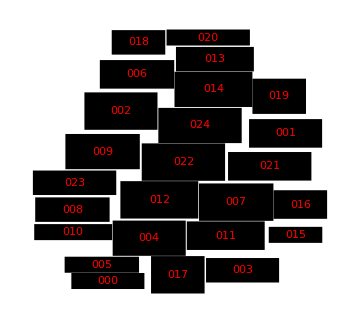

```mathematica
plot2=wordCloud[wordList1]
```

## Dynamic

#### Current word in the previous center

This function is limited to work with one static and next dynamic word cloud. But this handles the case of absent word.

```mathematica
centerSelection[wordListInit_,wordListCurrent_]:=
Module[{
w2=wordListSort[wordListCurrent],
w1 = finalWordPositionsStatic[wordListInit]},
Table[
w1⟦i⟧["Id"]==w2⟦j⟧["Id"],{j,Length[w2]},{i,Length[wordListInit]}
]//Boole
]

centroidList[wordListInit_,wordListCurrent_]:=
Module[{
center=myCentroid[finalWordPositionsStatic[wordListInit]],
cmatrix=centerSelection[wordListInit,wordListCurrent],
scale},
scale=√(Total[myArea/@wordListCurrent]/Total[myArea/@wordListInit]);
scale*(cmatrix.center)
]

wordInCentroid[wordListInit_,wordListCurrent_]:=Module[
{wl2=wordListSort[wordListCurrent],
wl1=centroidList[wordListInit,wordListCurrent]},
Table[myTranslate[wl2⟦i⟧,wl1⟦i⟧],{i,Length[wl2]}]
]
```

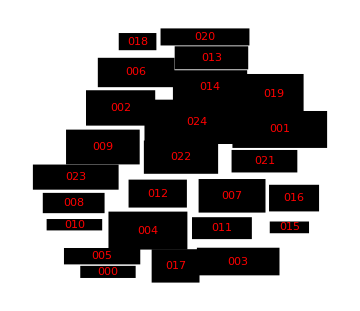

```mathematica
plot3=Graphics[toGraphic[wordInCentroid[wordList1,wordList2]],ImageSize->Medium,Frame->False]
```

We start with putting the word in their previous position. Next task is to remove the overlap.

```mathematica
{plot2,plot3}
```

{-Graphics-,-Graphics-}

### off grid

```mathematica
offCenterGrid[wordListInit_,wordListCurrent_]:=
Module[{
grid=spiralGrid[wordListCurrent],
center=centroidList[wordListInit,wordListCurrent],
bLimit=Max[Abs[spiralGrid[wordListCurrent]]],
xmin,ymin,xmax,ymax,
offGrid},
{xmin,ymin,xmax,ymax}={-bLimit,-bLimit,bLimit,bLimit};
offGrid=(Function[coord,#+coord]/@grid)&/@center;
Table[
Select[offGrid⟦i⟧, xmin<#⟦1⟧<xmax && ymin<#⟦2⟧<ymax&],{i,Dimensions[offGrid]⟦1⟧}
]
]
```

### Current Off Grid

```mathematica
positionCurrentWordDynamic[wordListInit_,wordListCurrent_,wordPosition_,currentWord_]:=
Module[{
ocg=offCenterGrid[wordListInit,wordListCurrent],
part=Length[wordPosition],
out,cog,cwog},
out=Not[RegionMember[RegionUnion[toRectangle@wordPosition⟦part⟧],ocg⟦part⟧]];
cog=Pick[ocg⟦part⟧,out];
cwog=myTranslate[currentWord,(#-cog⟦1⟧)]&/@cog;
SelectFirst[cwog,Not[intersectListQ[#,wordPosition]]&]
]
```

#### Dynamic word Cloud

```mathematica
finalWordPositionsDynamic[wordListInit_,wordListCurrent_]:=Fold[Append[#1,positionCurrentWordDynamic[wordListInit,wordListCurrent,#1,#2]]&,{wordInCentroid[wordListInit,wordListCurrent]⟦1⟧},wordInCentroid[wordListInit,wordListCurrent]⟦2;;⟧]

wordCloudDynamic[wordListInit_,wordListCurrent_]:=Graphics[toGraphic[finalWordPositionsDynamic[wordListInit,wordListCurrent]],ImageSize->Medium,Frame->False]
```

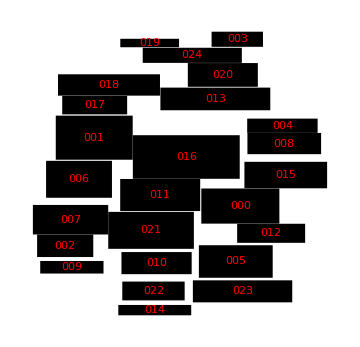
{192.219,-Graphics-}

```mathematica
plot4=wordCloudDynamic[wordList1,wordList2]
```

```mathematica
{plot2,plot4}
```

A plan to remove the white spaces in between is on the way.